Vectores aleatorios:

Sea (X,Y) un vector aleatorio con función de densidad conjunta 
f(x,y)=Piecewise[{{ay, x≥ 0, y≥ 0, xy≤ 2, y≤ 2x}, {0, en el resto}}]
a) Calcular la constante “a” para que f sea función de densidad de probabilidad
b) Representar el conjunto donde la densidad es distinta de cero
c) Representar la función de densidad

```mathematica
f[x_,y_]:=Piecewise[{{a y, x≥0&&y≥0&&x y≤2&&y⩽2 x}},0]
```

```mathematica
f[x,y]
```

Piecewise[{{a y, x≥0&&y≥0&&x y≤2&&y≤2 x}, {0, True}}]

Soporte de la distribución de la v.a. bidimensional (X, Y)

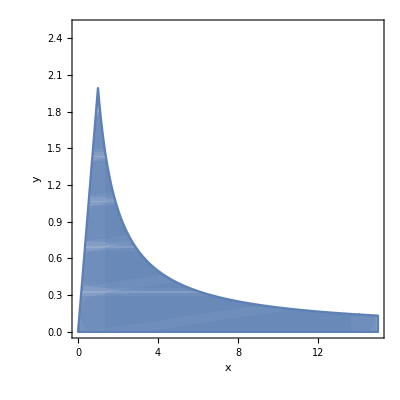

```mathematica
RegionPlot[x≥0&&y≥0&&x y≤2&&y⩽2 x,{x,0,15},{y,0,2.5},FrameLabel->{"x","y"},PlotPoints->300]
```

Evidentemente, los valores de x pueden ser  x ∈ [0, +∞), aunque la representación se realiza para 0 ≤ x ≤ 15

Cálculo de la constante “a”:
La función de densidad conjunta  verifica que la integral en todo ℝ^2 debe ser 1 y ser no negativa. Imponemos la condición de que la integral doble sea 1 y despejamos el valor de la constante a.

```mathematica
Solve[Integrate[f[x,y],{x,0,∞},{y,0,2}]==1,a]
```

{{a→3/8}}

Densidad conjunta

```mathematica
f[x_,y_]:=Piecewise[{{3 y/8, x≥0&&y≥0&&x y≤2&&y⩽2 x}},0]
```

```mathematica
Plot3D[f[x,y],{x,-1,10},{y,-0.5,3},PlotRange->All,PlotPoints->100,AxesLabel->{"x","y","f(x,y)"}]
```

-Graphics3D-

Marginales

```mathematica
marginalX=Integrate[f[x,y],{y,0,∞}]
```

Piecewise[{{3/(4 x^2), x>1}, {(3 x^2)/4, 0<x≤1}, {0, True}}]

```mathematica
marginalX=Integrate[f[x,y],{y,0,2}]//Simplify
```

Piecewise[{{3/(4 x^2), x≥1}, {(3 x^2)/4, 0<x<1}, {0, True}}]

Evidentemente es una función de densidad

```mathematica
Integrate[marginalX,{x,0,∞}]
```

1

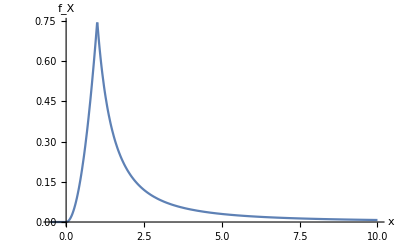

```mathematica
Plot[marginalX,{x,-0.5,10},PlotRange->All,AxesLabel->{"x","f_X"}]
```

```mathematica
marginalY=Integrate[f[x,y],{x,0,∞}]
```

Piecewise[{{-3/16 (-4+y^2), 0<y<2}, {0, True}}]

```mathematica
marginalYbis[y_]:=Integrate[f[x,y],{x,0,∞}]
```

```mathematica
marginalYbis[y]
```

Piecewise[{{-3/16 (-4+y^2), 0<y<2}, {0, True}}]

Evidentemente es una función de densidad

```mathematica
Integrate[marginalY,{y,0,2}]
```

1

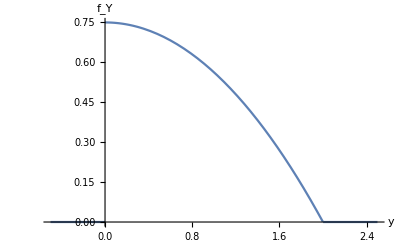

```mathematica
Plot[marginalYbis[y],{y,-.5,2.5},AxesLabel->{"y","f_Y"}]
```

```mathematica
Plot[marginalY,{y,-.5,2.5},AxesLabel->{"y","f_Y"}]
```

-Graphics-

Condicionadas
X | Y=y

```mathematica
fXdadoY[x_,y_]:=Piecewise[{{2 y/(4-y^2),y/2⩽x⩽2/y}},0]
```

```mathematica
fXdadoY[x,y]
```

Piecewise[{{(2 y)/(4-y^2), y/2≤x≤2/y}, {0, True}}]

X | Y=y ∼ U [y/2, 2/y]          para  0 < y < 2

Evidentemente son  funciones de densidad

```mathematica
Integrate[fXdadoY[x,y],{x,y/2,2/y},Assumptions->0<y<2]
```

1

Condicionadas,  
Y | X=x ,    si     0 < x ≤ 1

```mathematica
f1YdadoX[y_,x_]:=Piecewise[{{y/(2 x^2),0≤y≤2 x }},0]
```

```mathematica
f1YdadoX[y,x]
```

Piecewise[{{y/(2 x^2), 0≤y≤2 x}, {0, True}}]

Evidentemente son  funciones de densidad

```mathematica
Integrate[f1YdadoX[y,x],{y,0,2 x},Assumptions->0<x≤  1]
```

Condicionadas,  
Y | X=x ,    si      x ≥ 1

```mathematica
f2YdadoX[y_,x_]:=Piecewise[{{y x^2/2,0≤y<2/x}},0]
```

```mathematica
f2YdadoX[y,x]
```

Evidentemente son  funciones de densidad

```mathematica
Integrate[f2YdadoX[y,x],{y,0,2 x},Assumptions->x≥ 1]
```

Esperanzas marginales y condicionadas

```mathematica
esperanzaX=Integrate[x marginalX,{x,0,∞}]
```

La E[X] no es finita !!!!!

```mathematica
esperanzaY=Integrate[y marginalY,{y,0,2}]
```

```mathematica
esperanzaXdadoy=Integrate[x fXdadoY[x,y],{x,y/2,2/y},Assumptions->0<y<2]
```

```mathematica
esperanza1YdadoX=Integrate[y f1YdadoX[y,x],{y,0,2 x},Assumptions->0<x≤  1]
```

```mathematica
esperanza2YdadoX=Integrate[y f2YdadoX[y,x],{y,0,2 x},Assumptions->x≥ 1]
```